# Pole friendly P_1 solver

## P_1 ODE Quadratic Solver

The IVP is
	y'' | = | f(z,y) | = | 6 y^2+z  with y(0)=y_0 and y'(0)=v_0
We can compute 
	y''(0)=6(y(0))^2+0=6 y_0^2
and approximate 
	y(h)≈y_0+h v_0+0.5 h^2 y''(0)=y_0+h v_0+0.5 h^2 y_0^2. 
Converting this to a fixed step size ODE solver is not too bad.  The first step is 
	y_1 | = | y_0+h v_0+0.5 h^2 y''(z_0)  | = | y_0+h v_0+0.5 h^2 f(z_0,y_0) 
v_1 | = | v_0+h v'(z_0)                             | = | v_0+h f(z_0,y_0)                           
The iteration (with a fixed step size h) is

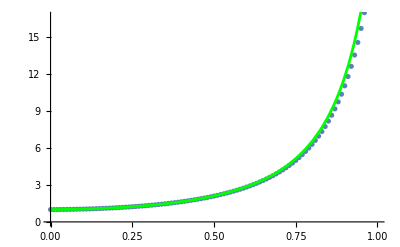

```mathematica
Clear[TwoStep]
TwoStep[h_][{zIn_,yIn_,vIn_}]:=Module[{y2d},
y2d=6 yIn^2+zIn;
 {zIn + h, yIn+h vIn + 0.5 h^2 y2d, vIn + h y2d}
]
{h,n}={0.01,100};
{z0,y0,v0}={0,1+0.01 I, 0.1}; TMax=(n+1) h;
TwoData=NestList[TwoStep[h],{0,y0,v0},n];
ySol=NDSolveValue[{ y''[t]==6 y[t]^2+t, y[0]==y0,y'[0]==v0},y,{t, 0,TMax} ];
Show[
ListPlot[Re[TwoData⟦All,{1,2}⟧]],
Plot[Re[ySol[t]],{t,0, TMax},PlotStyle->Green]
]
```

There are two obvious problems with this:  the step is not accurate enough and the algorithm has no mechanism to estimate or adjust h.  There is a more subtle problem: the real solution does not look at all like a polynomial.

## P_1 ODE Taylor Series Solver

The ODE is
	y''=6 y^2+z  with y(0)=y_0 and y'(0)=v_0
we can differentiate to get
	y''' | = | 12y y'+1
y'''' | = | 12(y y''+(y')^2)
y''''' | = | 12 (y y'''+3y' y'')
… |   |  
We can  compute as many derivatives as we want and construct the Taylor Series approximation
	y(h) | ≈ | y_0+h v_0+1/2 h^2y''(0)+1/(3!)h^3 y'''(0)+1/(4!)h^4 y''''(0)+1/(5!)h^5 y'''''(0)	
this will presumably be more accurate than the quadratic approximation.

```mathematica
Clear[FiveStep]
FiveStep[h_][{zIn_,yIn_,vIn_}]:=Module[{y2d,y3d,y4d,y5d},
y2d=6 yIn^2+zIn;
y3d=12 yIn vIn+1;
y4d = 12(yIn y2d+vIn^2);
y5d = 12(yIn y3d + 3 vIn y2d);
 {zIn + h, 
yIn+h vIn + 0.5 h^2 y2d+1/(3!)h^3 y3d+1/(4!)h^4 y4d+1/(5!)h^5 y5d, 
vIn + h y2d + 0.5 h^2 y3d + 1/(3!)h^3 y4d+ 1/(4!)h^4 y5d}]
```

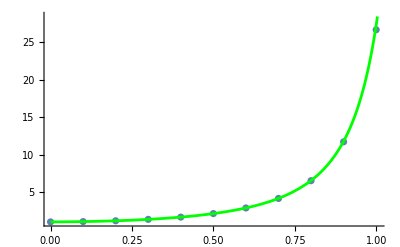

```mathematica
{h,n}={0.1,10};
{z0,y0,v0}={0,1+0.01 I, 0.1}; TMax=(n+1) h;
FiveData=NestList[FiveStep[h],{0,y0,v0},n];
ySol=NDSolveValue[{ y''[t]==6 y[t]^2+t, y[0]==y0,y'[0]==v0},y,{t, 0,TMax} ];
Show[
ListPlot[Re[FiveData⟦All,{1,2}⟧]],
Plot[Re[ySol[t]],{t,0, TMax},PlotStyle->Green],
PlotRange->All
]
```

Although each step is about 4 times as much work I can take ten times fewer steps and get a better answer!  The fancier algorithm should take about 4/10 the time.

## P_1 ODE Taylor Series Solver Step size control

The Taylor Series approximation
	y(h) | ≈ | y_0+h v_0+1/2 h^2y''(0)+1/(3!)h^3 y'''(0)+1/(4!)h^4 y''''(0)+1/(5!)h^5 y'''''(0)	
comes with a built in approximate error estimate since
	y(h) | = | y_0+h v_0+1/2 h^2y''(0)+1/(3!)h^3 y'''(0)+1/(4!)h^4 y''''(0)+1/(5!)h^5 y'''''(τ h)	
for some 0≤τ≤1.  The idea is that 
	1/(5!)h^5 y'''''(τ h)≈1/(5!)h^5 y'''''(0)
provides an error estimate for the fourth order polynomial
	y_0+h v_0+1/2 h^2y''(0)+1/(3!)h^3 y'''(0)+1/(4!)h^4 y''''(0) 
You can choose h so that the absolute tolerance 
	|1/(5!)h^5 y'''''(0)|<Tol
is satisfied.  You probably should choose h so that the relative tolerance
	(|1/(5!)h^5 y'''''(0)|)/y_0<Tol
is satisfied.  The logic of this probably argues for the quadratic update
	y_0+h v_0+1/2 h^2 y''(0)+1/(3!)h^3 y'''(0)+1/(4!)h^4 y''''(0) .
However, all practical code implementations use the higher order update.  This is called local extrapolation.  Step size control of this sort is always implemented with a safety factor called 0<γ<1 in the computation. For y the absolute error step size control looks like
	|1/(5!)h^5 y'''''(0)|=γ Tol | ⟹ | h=(γ (5!)/(|y'''''(0)|) )^(1/5).
For the derivative y' this looks like  
	|1/(4!)h^4 y'''''(0)|=γ Tol | ⟹h= | (γ (4!)/(|y'''''(0)|) )^(1/4)
You could work out where these switch over but there is no need.  A standard thing to do is to just take the smallest of these two step sizes. A maximum step size is also almost always imposed.

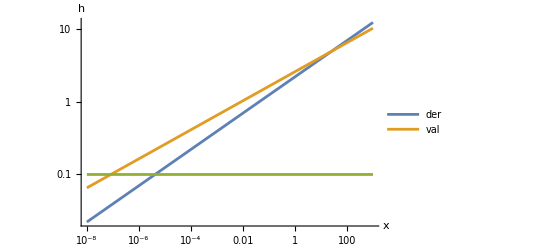

```mathematica
LogLogPlot[{(4! x)^(1/4),(5! x)^(1/5),0.1},{x,0.00000001, 1000},
PlotRange->All,
PlotLegends->{"der","val","max"},
AxesLabel->{"x","h"}
]
```

```mathematica
Clear[FiveStepTol]
FiveStepTol[Tol_][{zIn_,yIn_,vIn_}]:=Module[{y2d,y3d,y4d,y5d,h,γ=0.9},
y2d=6 yIn^2+zIn;
y3d=12 yIn vIn+1;
y4d = 12(yIn y2d+vIn^2);
y5d = 12(yIn y3d + 3 vIn y2d);
h = Min[0.1,(γ (4!)/Abs[y5d] )^(1/4),(γ (5!)/Abs[y5d] )^(1/5)];
 {zIn + h, 
yIn+h vIn + 0.5 h^2 y2d+1/(3!)h^3 y3d+1/(4!)h^4 y4d+1/(5!)h^5 y5d, 
vIn + h y2d + 0.5 h^2 y3d + 1/(3!)h^3 y4d+ 1/(4!)h^4 y5d}]
```

Now it is doing a good job of tracking the curve with small steps where needed.

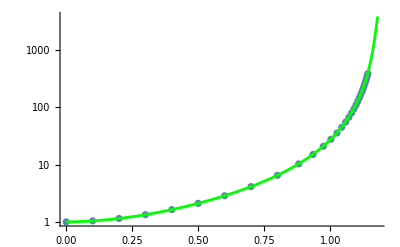

```mathematica
n=5;
{z0,y0,v0}={0,1+0.01 I, 0.1}; TMax=1.18;
Tol=10.0^-14;
FiveData=NestList[FiveStepTol[Tol],{0,y0,v0},30];
ySol=NDSolveValue[{ y''[t]==6 y[t]^2+t, y[0]==y0,y'[0]==v0},y,{t, 0,TMax} ];
Show[
ListLogPlot[Re[FiveData⟦All,{1,2}⟧]],
LogPlot[Re[ySol[t]],{t,0, TMax},PlotStyle->Green,PlotRange->All],
PlotRange->All
]
```

Although each step is about 4 times as much work I can take ten times fewer steps and get a better answer!  The fancier algorithm should take about 4/10 the time.

## P_1 ODE Taylor Series Solver Target Interval and Step size control

The Taylor Series approximation
	y(h) | ≈ | y_0+h v_0+1/2 h^2y''(0)+1/(3!)h^3 y'''(0)+1/(4!)h^4 y''''(0)+1/(5!)h^5 y'''''(0)	
comes with a built in approximate error estimate since
	y(h) | = | y_0+h v_0+1/2 h^2y''(0)+1/(3!)h^3 y'''(0)+1/(4!)h^4 y''''(0)+1/(5!)h^5 y'''''(τ h)	
for some 0≤τ≤1.  The idea is that 
	1/(5!)h^5 y'''''(τ h)≈1/(5!)h^5 y'''''(0)
provides an error estimate for the fourth order polynomial
	y_0+h v_0+1/2 h^2y''(0)+1/(3!)h^3 y'''(0)+1/(4!)h^4 y''''(0) 
You can choose h so that the absolute tolerance 
	|1/(5!)h^5 y'''''(0)|<Tol
is satisfied.  You probably should choose h so that the relative tolerance
	(|1/(5!)h^5 y'''''(0)|)/y_0<Tol
is satisfied.  The logic of this probably argues for the quadratic update
	y_0+h v_0+1/2 h^2 y''(0)+1/(3!)h^3 y'''(0)+1/(4!)h^4 y''''(0) .
However, all practical code implementations use the higher order update.  This is called local extrapolation.  Step size control of this sort is always implemented with a safety factor called 0<γ<1 in the computation. For y the absolute error step size control looks like
	|1/(5!)h^5 y'''''(0)|=γ Tol | ⟹ | h=(γ (5!)/(|y'''''(0)|) )^(1/5).
For the derivative y' this looks like  
	|1/(4!)h^4 y'''''(0)|=γ Tol | ⟹h= | (γ (4!)/(|y'''''(0)|) )^(1/4)
You could work out where these switch over but there is no need.  A standard thing to do is to just take the smallest of these two step sizes. A maximum step size is also almost always imposed.

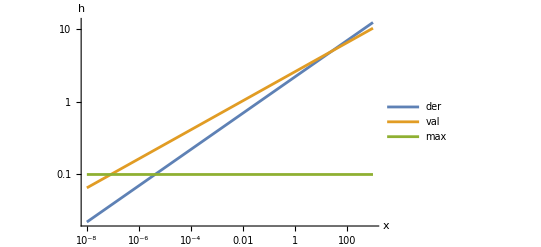

```mathematica
LogLogPlot[{(4! x)^(1/4),(5! x)^(1/5),0.1},{x,0.00000001, 1000},
PlotRange->All,
PlotLegends->{"der","val","max"},
AxesLabel->{"x","h"}
]
```

Our step size control Stepper for P_1 is

```mathematica
Clear[FiveStepTol]
FiveStepTol[Tol_][{zIn_,yIn_,vIn_}]:=Module[
{y2d,y3d,y4d,y5d,h,γ=0.9, MaxStep=0.1},
y2d=6 yIn^2+zIn;
y3d=12 yIn vIn+1;
y4d = 12(yIn y2d+vIn^2);
y5d = 12(yIn y3d + 3 vIn y2d);
h = Min[MaxStep,(γ (4!)/Abs[y5d] )^(1/4),(γ (5!)/Abs[y5d] )^(1/5)];
 {zIn + h, 
yIn+h vIn + 0.5 h^2 y2d+1/(3!)h^3 y3d+1/(4!)h^4 y4d+1/(5!)h^5 y5d, 
vIn + h y2d + 0.5 h^2 y3d + 1/(3!)h^3 y4d+ 1/(4!)h^4 y5d}]
```

All we need to do to make it useful is to run it up to a target maximum interval.

```mathematica
n=5;
{z0,y0,v0}={0,1+0.01 I, 0.1}; TMax=1.18;
Tol=10.0^-10;
FiveData=NestWhileList[FiveStepTol[Tol],{0,y0,v0},(#⟦1⟧<TMax)&];
ySol=NDSolveValue[{ y''[t]==6 y[t]^2+t, y[0]==y0,y'[0]==v0},y,{t, 0,TMax} ];
TabView[{
"y"->Show[
ListLogPlot[Re[FiveData⟦All,{1,2}⟧],PlotRange->All],
LogPlot[Re[ySol[t]],{t,0, TMax},PlotStyle->Green,PlotRange->All],
PlotRange->All,
PlotLabel->Length[FiveData]
],
"v"->Show[
ListLogPlot[Re[FiveData⟦All,{1,3}⟧],PlotRange->All],
LogPlot[Re[ySol'[t]],{t,0, TMax},PlotStyle->Green,PlotRange->All],
PlotRange->All,
PlotLabel->Length[FiveData]]}]
```

12

This looks like it is working OK.  Here are some questions. What would happen to the step size if I made the error a relative error? Can we trust the solver Mathematica is using? What solver is Mathematica using? Can we change the solver Mathematica is using? Would we get the same answer in Julia, matlab, Python, etc?

## Pade Approximation vs Taylor Series: Big Picture

The analytical solution of P_1 has lots of double poles (but no branch cuts) in the complex plane.  The path we have been using along the real axis coms close to one of the poles. Here is the Taylor series solver running over the near pole.  To me it is amazing that it managed to track the solution through the “spike” at all!

```mathematica
{z0,y0,v0}={0,1+0.01 I, 0.1}; TMax=1.2;
Tol=10.0^-10;
FiveData=NestWhileList[FiveStepTol[Tol],{0,y0,v0},(#⟦1⟧<TMax)&];
ySol=NDSolveValue[{ y''[t]==6 y[t]^2+t, y[0]==y0,y'[0]==v0},y,{t, 0,TMax} ];
TabView[{
"y"->Show[
ListLogPlot[Re[FiveData⟦All,{1,2}⟧],PlotRange->All],
LogPlot[Re[ySol[t]],{t,0, TMax},PlotStyle->Green,PlotRange->All],
PlotRange->All,
PlotLabel->Length[FiveData]
],
"v"->Show[
ListLogPlot[Re[FiveData⟦All,{1,3}⟧],PlotRange->All],
LogPlot[Re[ySol'[t]],{t,0, TMax},PlotStyle->Green,PlotRange->All],
PlotRange->All,
PlotLabel->Length[FiveData]]}]
```

12

If the real solution has a pole then maybe our approximate solution should have a pole!  The first thing we need to know how to do is produce a rational function that fits derivative data.  This is called a Pade approximant. https://en.wikipedia.org/wiki/Pad%C3%A9_approximant.  The Mathematica command is PadeApproximant. The improvement a rational approximation makes for an appropriate function is amazing!

```mathematica
Clear[f,t,z]
{n,m}={2,6}
f[z_]:=Sin[z]/(0.05+(z-0.5)^2) 
t[z_]=Normal[Series[f[z],{z,0,m+n}]];
p[z_]=PadeApproximant[f[z],{z,0,{m,n}}];
SetOptions[LogPlot,GridLines->Automatic,Frame->True];
TabView[{
"fun"->Plot[{f[z],t[z],p[z]},{z,0,2},PlotRange->{-2,12},
PlotLegends->{"f","t_(m + n)","p_(m/n)"}],
"err"->LogPlot[{Abs[f[z]-t[z]],Abs[f[z]-p[z]]},{z,0,2},
PlotLegends->{"|f-t_(m + n)|","|f-p_(m/n)|"}],
"rel err"->LogPlot[{Abs[1-t[z]/f[z]],Abs[1-p[z]/f[z]]},{z,0,2},
PlotLegends->{"|f-t_(m + n)|/|f|","|f-p_(m/n)|/|f|"}],
"errs p"->LogPlot[{Abs[1-p[z]/f[z]],Abs[f[z]-p[z]]},{z,0,2},
PlotLegends->{"|f-p_(m/n)|/|f|","|f-p_(m/n)|"}]
}]
```

{2,6}

1234

## Pade Approximation from Taylor Series: Computation

There are several ways to think about converting a rational function to and from a polynomial. We want 
	f(x)=c_0+x c_1+x^2 c_2+x^3 c_3+… ≈(a_0+x a_1+x^2 a_2+…)/(b_0+x b_1+x^2 b_2+…) 
It is common to normalize by choosing b_0=1.  Note, other normalizations are used.  The c coefficients are determined from the derivatives of f.  We want a way to compute the a and b coefficients.

We need to decide how many c coefficients we have.  We need to work out how many a and b coefficients we can determine. With b_0=1  there are n+m+1 coefficients in 
	 (a_0+x a_1+x^2 a_2+…+x^n a_n)/(1+x b_1+x^2 b_2+…+x^m b_m).
We should be able to choose these to match the first n+m+1 c coefficients i.e. 
	c_0+x c_1+x^2 c_2+x^3 c_3+…+c_(n+m)x^(n+m)+…=(a_0+x a_1+x^2 a_2+…+x^n a_n)/(1+x b_1+x^2 b_2+…+x^m b_m)
Going back to the version with b_0 and cross multiplying to remove the fraction gives
	(∑_(i=0)^(m+n) c_i x^i+O(x^(m+n+1)))(b_0+∑_(i=1)^m b_i x^i)=∑_(i=0)^n a_i x^i
It is easier to think about this as just a set of linear equations relating the coefficient vectors a and b. For n=2 and m=6 multiplying out and equating coefficients gives the 8 equations

x^(RowBox[{) | a_0==b_0 c_0
x^(RowBox[{) | a_1==b_1 c_0+b_0 c_1
x^(RowBox[{) | a_2==b_2 c_0+b_1 c_1+b_0 c_2
x^(RowBox[{) | a_3==b_3 c_0+b_2 c_1+b_1 c_2+b_0 c_3
x^(RowBox[{) | a_4==b_4 c_0+b_3 c_1+b_2 c_2+b_1 c_3+b_0 c_4
x^(RowBox[{) | a_5==b_5 c_0+b_4 c_1+b_3 c_2+b_2 c_3+b_1 c_4+b_0 c_5
x^(RowBox[{) | a_6==b_6 c_0+b_5 c_1+b_4 c_2+b_3 c_3+b_2 c_4+b_1 c_5+b_0 c_6
x^(RowBox[{) | a_7==b_6 c_1+b_5 c_2+b_4 c_3+b_3 c_4+b_2 c_5+b_1 c_6+b_0 c_7
x^(RowBox[{) | a_8==b_6 c_2+b_5 c_3+b_4 c_4+b_3 c_5+b_2 c_6+b_1 c_7+b_0 c_8

Organizing this we see the linear system 
	C_top.b=a 
where C_top is a stripey (n+1)×(n+1)Toeplitz matrix
	(c_0 | 0 | 0 | 0 | 0 | 0 | 0
c_1 | c_0 | 0 | 0 | 0 | 0 | 0
c_2 | c_1 | c_0 | 0 | 0 | 0 | 0
c_3 | c_2 | c_1 | c_0 | 0 | 0 | 0
c_4 | c_3 | c_2 | c_1 | c_0 | 0 | 0
c_5 | c_4 | c_3 | c_2 | c_1 | c_0 | 0
c_6 | c_5 | c_4 | c_3 | c_2 | c_1 | c_0
c_7 | c_6 | c_5 | c_4 | c_3 | c_2 | c_1
c_8 | c_7 | c_6 | c_5 | c_4 | c_3 | c_2)	
and the vectors a and b are the vectors
	a=(a_0
a_1
⋮
a_n
0
⋮
0) and b=(b_0
b_1
⋮
b_n) 
The bottom

```mathematica
{m,n}={2,6};
Clear[a,b,c,aVec,bVec,cVec]
aVec=Table[Subscript[a, i],{i,0,m}];
bVec=Table[Subscript[b, i],{i,0,n}];
cVec=Table[Subscript[c, i],{i,0,m+n}];
CMat=LowerTriangularize[ToeplitzMatrix[cVec,cVec⟦1;;n+1⟧]];
MatrixForm[CMat]
TableForm[CMat.bVec]
```

(c_0 | 0 | 0 | 0 | 0 | 0 | 0
c_1 | c_0 | 0 | 0 | 0 | 0 | 0
c_2 | c_1 | c_0 | 0 | 0 | 0 | 0
c_3 | c_2 | c_1 | c_0 | 0 | 0 | 0
c_4 | c_3 | c_2 | c_1 | c_0 | 0 | 0
c_5 | c_4 | c_3 | c_2 | c_1 | c_0 | 0
c_6 | c_5 | c_4 | c_3 | c_2 | c_1 | c_0
c_7 | c_6 | c_5 | c_4 | c_3 | c_2 | c_1
c_8 | c_7 | c_6 | c_5 | c_4 | c_3 | c_2)

b_0 c_0
b_1 c_0+b_0 c_1
b_2 c_0+b_1 c_1+b_0 c_2
b_3 c_0+b_2 c_1+b_1 c_2+b_0 c_3
b_4 c_0+b_3 c_1+b_2 c_2+b_1 c_3+b_0 c_4
b_5 c_0+b_4 c_1+b_3 c_2+b_2 c_3+b_1 c_4+b_0 c_5
b_6 c_0+b_5 c_1+b_4 c_2+b_3 c_3+b_2 c_4+b_1 c_5+b_0 c_6
b_6 c_1+b_5 c_2+b_4 c_3+b_3 c_4+b_2 c_5+b_1 c_6+b_0 c_7
b_6 c_2+b_5 c_3+b_4 c_4+b_3 c_5+b_2 c_6+b_1 c_7+b_0 c_8

```mathematica
TableForm[CMat.bVec]
```

(c_0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
c_1 | c_0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
c_2 | c_1 | c_0 | 0 | 0 | 0 | 0 | 0 | 0
c_3 | c_2 | c_1 | c_0 | 0 | 0 | 0 | 0 | 0
c_4 | c_3 | c_2 | c_1 | c_0 | 0 | 0 | 0 | 0
c_5 | c_4 | c_3 | c_2 | c_1 | c_0 | 0 | 0 | 0
c_6 | c_5 | c_4 | c_3 | c_2 | c_1 | c_0 | 0 | 0
c_7 | c_6 | c_5 | c_4 | c_3 | c_2 | c_1 | c_0 | 0
c_8 | c_7 | c_6 | c_5 | c_4 | c_3 | c_2 | c_1 | c_0)

Dot::dotsh: Tensors {{c_0,0,0,0,0,0,0,0,0},{c_1,c_0,0,0,0,0,0,0,0},{c_2,c_1,c_0,0,0,0,0,0,0},{c_3,c_2,c_1,c_0,0,0,0,0,0},{c_4,c_3,c_2,c_1,c_0,0,0,0,0},{c_5,c_4,c_3,c_2,c_1,c_0,0,0,0},{c_6,c_5,c_4,c_3,c_2,c_1,c_0,0,0},{c_7,c_6,c_5,c_4,c_3,c_2,c_1,c_0,0},{c_8,c_7,c_6,c_5,c_4,c_3,c_2,c_1,c_0}} and {b_0,b_1,b_2,b_3,b_4,b_5,b_6} have incompatible shapes.

{{c_0,0,0,0,0,0,0,0,0},{c_1,c_0,0,0,0,0,0,0,0},{c_2,c_1,c_0,0,0,0,0,0,0},{c_3,c_2,c_1,c_0,0,0,0,0,0},{c_4,c_3,c_2,c_1,c_0,0,0,0,0},{c_5,c_4,c_3,c_2,c_1,c_0,0,0,0},{c_6,c_5,c_4,c_3,c_2,c_1,c_0,0,0},{c_7,c_6,c_5,c_4,c_3,c_2,c_1,c_0,0},{c_8,c_7,c_6,c_5,c_4,c_3,c_2,c_1,c_0}}.{b_0,b_1,b_2,b_3,b_4,b_5,b_6}

```mathematica
CMat=SparseArray[Band[],{n+m,m}]
```

```mathematica
MatrixForm[ToeplitzMatrix[Table[Subscript[c, i],{i,0,m}],SparseArray[1->Subscript[c, 0],m+n]]]
```

(c_0 | c_1 | c_2 | c_3 | c_4 | c_5 | c_6
c_1 | c_0 | c_1 | c_2 | c_3 | c_4 | c_5
c_2 | c_1 | c_0 | c_1 | c_2 | c_3 | c_4
c_3 | c_2 | c_1 | c_0 | c_1 | c_2 | c_3
c_4 | c_3 | c_2 | c_1 | c_0 | c_1 | c_2
c_5 | c_4 | c_3 | c_2 | c_1 | c_0 | c_1
c_6 | c_5 | c_4 | c_3 | c_2 | c_1 | c_0)

```mathematica
Information[ToeplitzMatrix]
```

```mathematica
{n,m}
Hmm=Expand[(∑_(i=0)^(m+n) Subscript[c, i] x^i)((∑_(i=0)^m Subscript[b, i] x^i))];
TableForm[
Table[Subscript[a, i]==Coefficient[Hmm,x,i],{i,0, n+m}],
TableHeadings->{Table[StringForm["x^(``)",i],{i, 0,n+m}]}
]
```

{2,6}

x^(RowBox[{) | a_0==b_0 c_0
x^(RowBox[{) | a_1==b_1 c_0+b_0 c_1
x^(RowBox[{) | a_2==b_2 c_0+b_1 c_1+b_0 c_2
x^(RowBox[{) | a_3==b_3 c_0+b_2 c_1+b_1 c_2+b_0 c_3
x^(RowBox[{) | a_4==b_4 c_0+b_3 c_1+b_2 c_2+b_1 c_3+b_0 c_4
x^(RowBox[{) | a_5==b_5 c_0+b_4 c_1+b_3 c_2+b_2 c_3+b_1 c_4+b_0 c_5
x^(RowBox[{) | a_6==b_6 c_0+b_5 c_1+b_4 c_2+b_3 c_3+b_2 c_4+b_1 c_5+b_0 c_6
x^(RowBox[{) | a_7==b_6 c_1+b_5 c_2+b_4 c_3+b_3 c_4+b_2 c_5+b_1 c_6+b_0 c_7
x^(RowBox[{) | a_8==b_6 c_2+b_5 c_3+b_4 c_4+b_3 c_5+b_2 c_6+b_1 c_7+b_0 c_8

```mathematica
Sum[Subscript[b, i] x^i,{i,0,5}]
```

b_0+x b_1+x^2 b_2+x^3 b_3+x^4 b_4+x^5 b_5

```mathematica
{z0,y0,v0}={0,1+0.01 I, 0.1}; TMax=1.2;
Tol=10.0^-10;
FiveData=NestWhileList[FiveStepTol[Tol],{0,y0,v0},(#⟦1⟧<TMax)&];
ySol=NDSolveValue[{ y''[t]==6 y[t]^2+t, y[0]==y0,y'[0]==v0},y,{t, 0,TMax} ];
TabView[{
"y"->Show[
ListLogPlot[Re[FiveData⟦All,{1,2}⟧],PlotRange->All],
LogPlot[Re[ySol[t]],{t,0, TMax},PlotStyle->Green,PlotRange->All],
PlotRange->All,
PlotLabel->Length[FiveData]
],
"v"->Show[
ListLogPlot[Re[FiveData⟦All,{1,3}⟧],PlotRange->All],
LogPlot[Re[ySol'[t]],{t,0, TMax},PlotStyle->Green,PlotRange->All],
PlotRange->All,
PlotLabel->Length[FiveData]]}]
```

12

If the real solution has a pole then maybe our approximate solution should have a pole!  The first thing we need to know how to do is produce a rational function that fits derivative data.  This is called a Pade approximant. https://en.wikipedia.org/wiki/Pad%C3%A9_approximant.  The Mathematica command is PadeApproximant. The improvement a rational approximation makes for an appropriate function is amazing!

```mathematica
Clear[f,t,z]
{n,m}={2,6}
f[z_]:=Sin[z]/(0.05+(z-0.5)^2) 
t[z_]=Normal[Series[f[z],{z,0,m+n}]];
p[z_]=PadeApproximant[f[z],{z,0,{m,n}}];
SetOptions[LogPlot,GridLines->Automatic,Frame->True];
TabView[{
"fun"->Plot[{f[z],t[z],p[z]},{z,0,2},PlotRange->{-2,12},
PlotLegends->{"f","t_(m + n)","p_(m/n)"}],
"err"->LogPlot[{Abs[f[z]-t[z]],Abs[f[z]-p[z]]},{z,0,2},
PlotLegends->{"|f-t_(m + n)|","|f-p_(m/n)|"}],
"rel err"->LogPlot[{Abs[1-t[z]/f[z]],Abs[1-p[z]/f[z]]},{z,0,2},
PlotLegends->{"|f-t_(m + n)|/|f|","|f-p_(m/n)|/|f|"}],
"errs p"->LogPlot[{Abs[1-p[z]/f[z]],Abs[f[z]-p[z]]},{z,0,2},
PlotLegends->{"|f-p_(m/n)|/|f|","|f-p_(m/n)|"}]
}]
```

{2,6}

1234